```mathematica
ClearAll
```

ClearAll

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma[a];
```

```mathematica
om=0.3;
gamma0=0.55;
gammap0=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

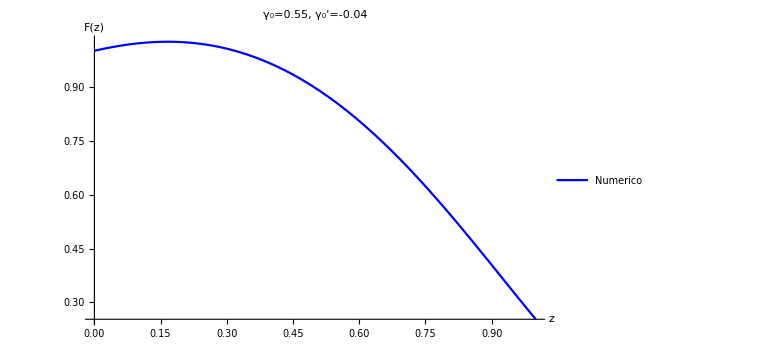

```mathematica
p1=Plot[Fz[z],{z,0,1}, PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

```mathematica
points=Table[{z,Fz[z]},{z,0,1,0.01}];
```

```mathematica
fit1=Fit[points, {1,z,z^2},z];
res1=Fit[points, {1,z,z^2},z,"FitResiduals"];
pointsfit=Table[{z,fit1},{z,0,1,0.01}];
```

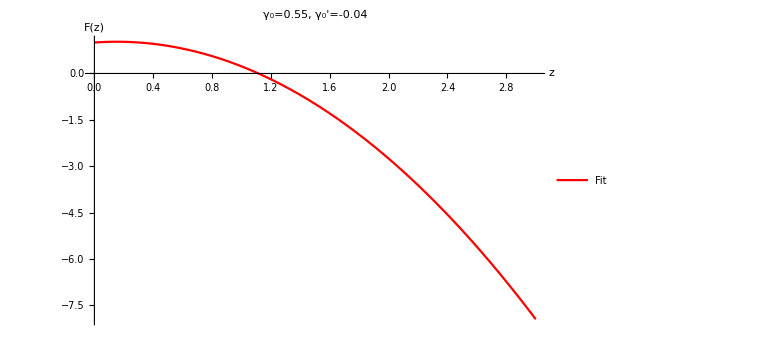

```mathematica
fit=Plot[fit1,{z,0,3}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

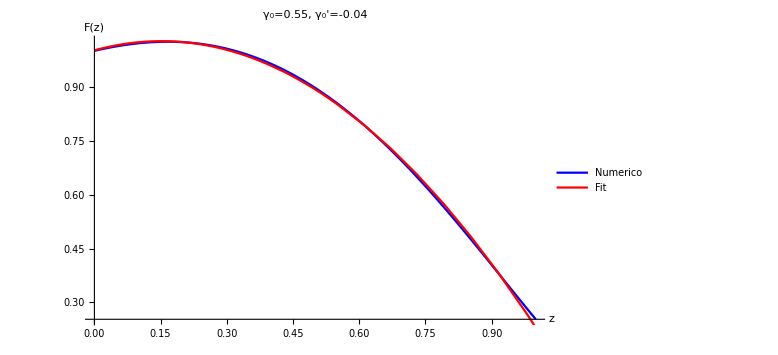

```mathematica
Show[p1,fit]
```

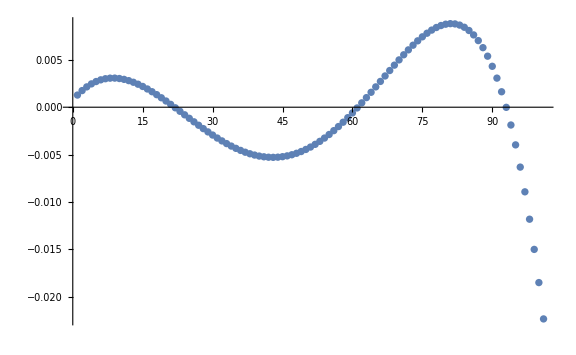

```mathematica
plotres1=ListPlot[res1, ImageSize->Large]
```

```mathematica
dif[z_]=1-fit1/Fz[z]
```

1-(1.00128+0.336927 z-1.10728 z^2)/(InterpolatingFunction[…][1/(1+z)])

```mathematica
Res6=Table[{z,dif[z]},{z,0,1,0.01}];
```

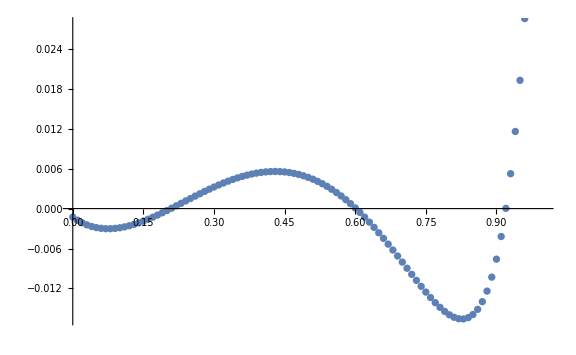

```mathematica
ListPlot[Res6, ImageSize->Large]
```

```mathematica
PearsonChiSquareTest[pointsfit,points]
```

0.999988

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=1.001283893224917+0.3369271691259142 z-1.1072791685116707 z^2
```

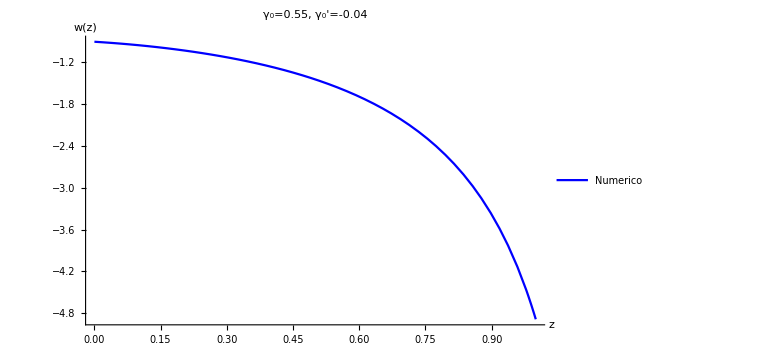

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

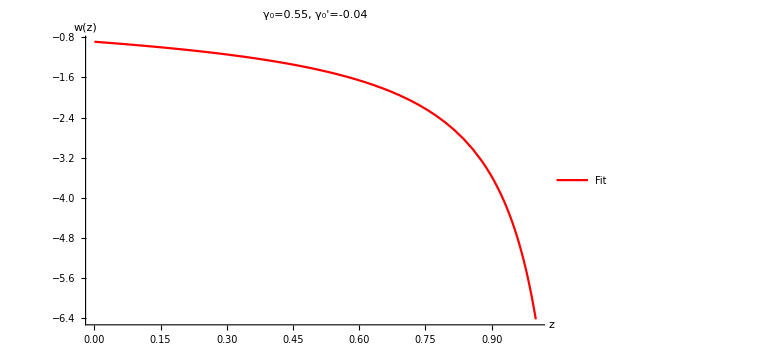

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

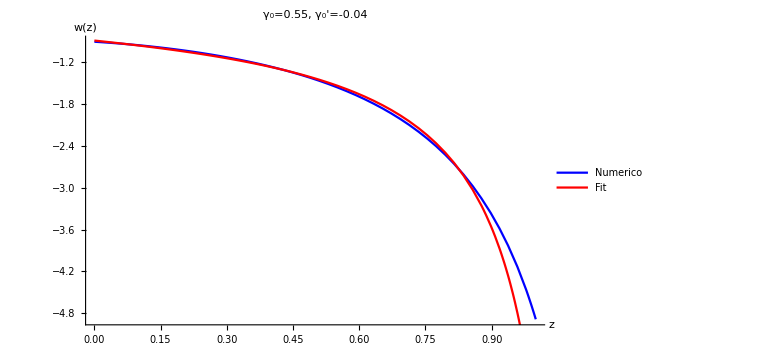

```mathematica
plot1=Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

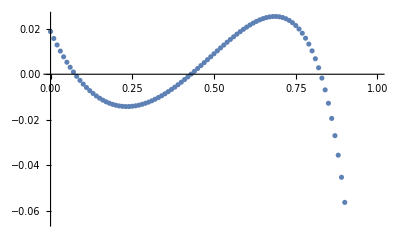

```mathematica
plotres=ListPlot[Res7]
```

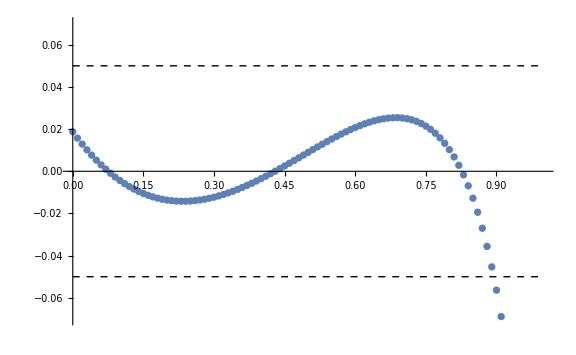

```mathematica
plot2=Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
fit2=Fit[points, {1,z,z^2,z^3},z]
```

0.990883+0.464927 z-1.42888 z^2+0.214398 z^3

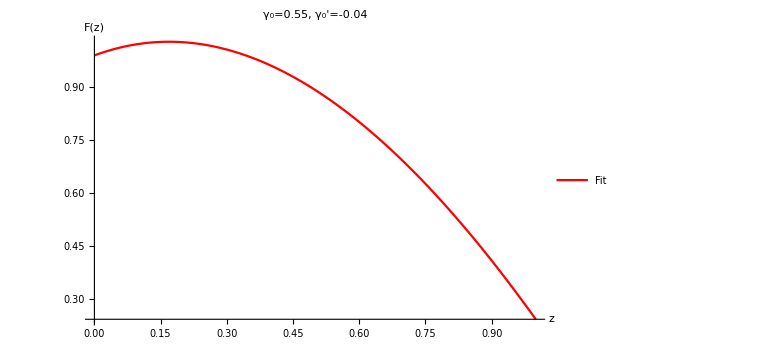

```mathematica
fit=Plot[fit2,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

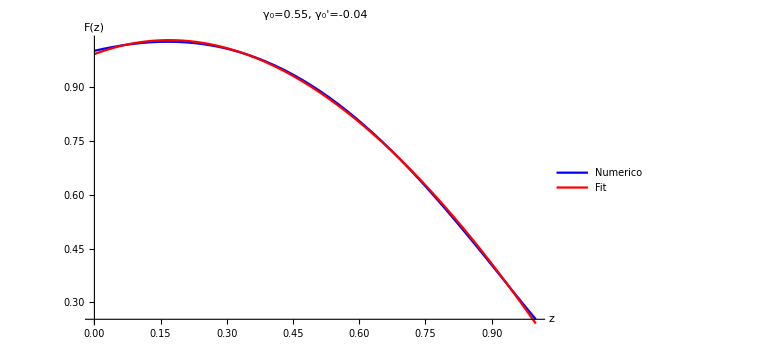

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit2=Table[{z,fit2},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit2,points]
```

0.999848

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9908834540260197+0.46492696732270133 z-1.4288759279086425 z^2+0.21439783959798006 z^3
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

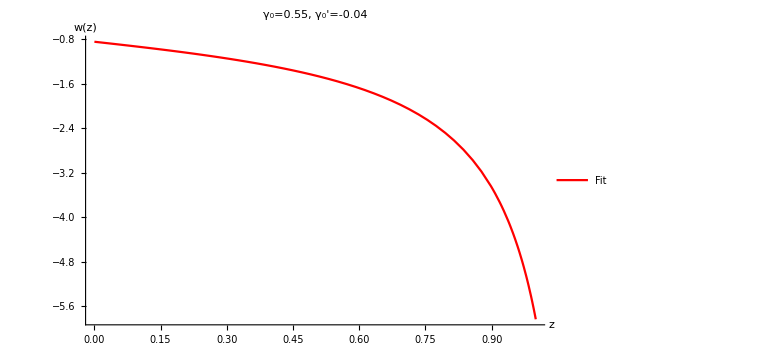

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

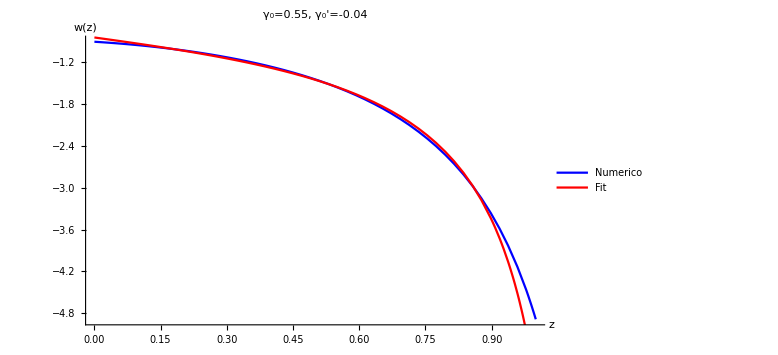

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

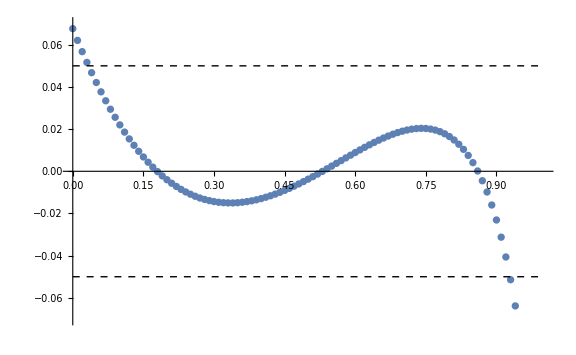

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
fit3=Fit[points, {1,z,z^2,z^3,z^4},z]
```

1.00122+0.248463 z-0.443444 z^2-1.32354 z^3+0.768967 z^4

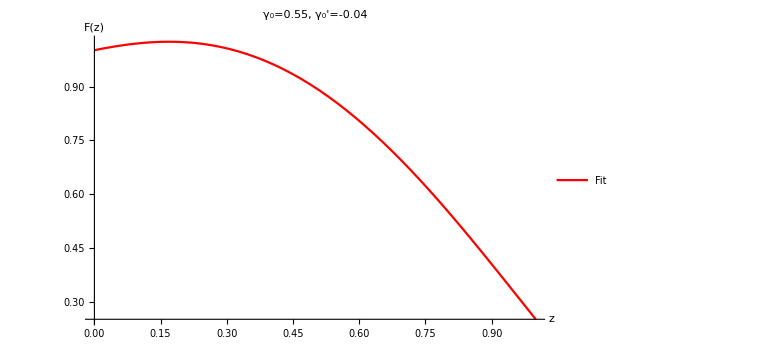

```mathematica
fit=Plot[fit3,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

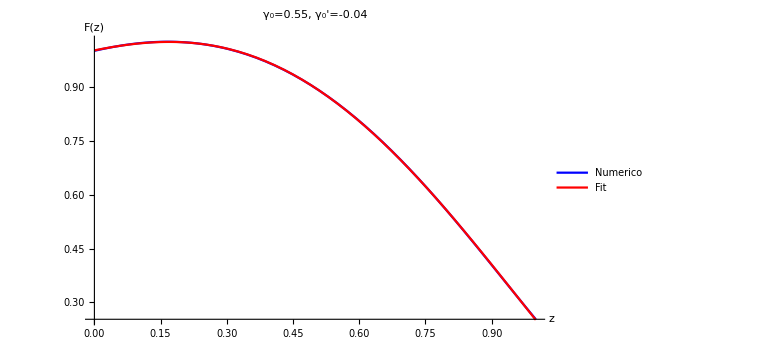

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit3=Table[{z,fit3},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit3,points]
```

1.

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=1.0012216043534157+0.24846266917464244 z-0.44344431839980764 z^2-1.3235367831235743 z^3+0.7689673113607776 z^4
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

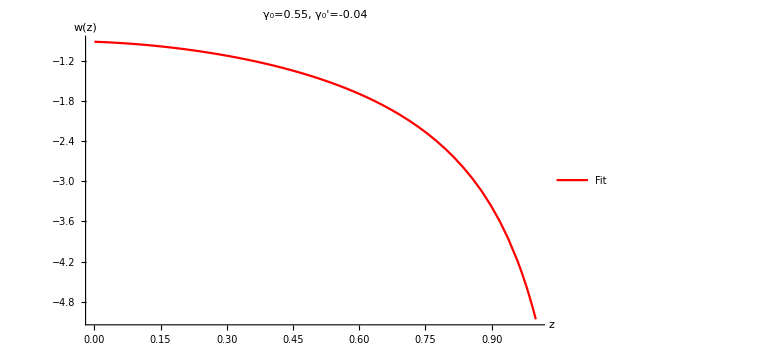

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

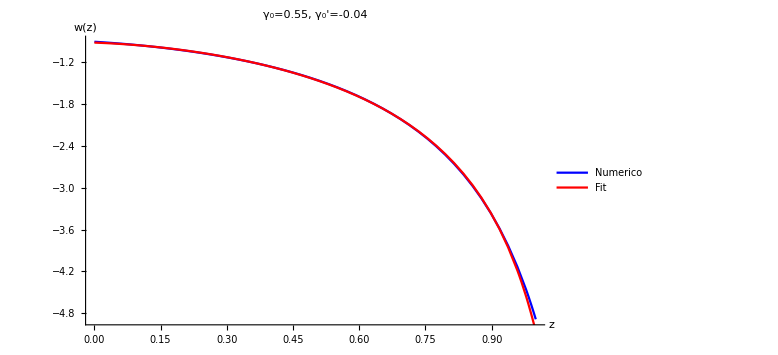

```mathematica
Show[wnum,wpol]
```

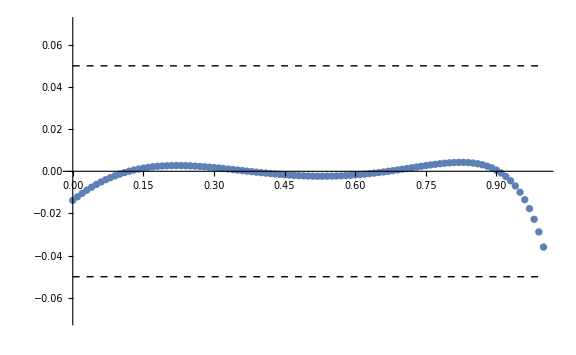

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
fit4=Fit[points, {1,z,z^2,z^3,z^4,z^5},z]
```

0.999825+0.293482 z-0.764868 z^2-0.460109 z^3-0.20475 z^4+0.389487 z^5

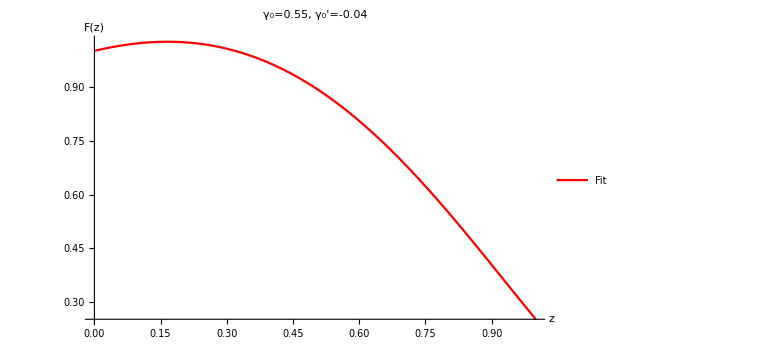

```mathematica
fit=Plot[fit4,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

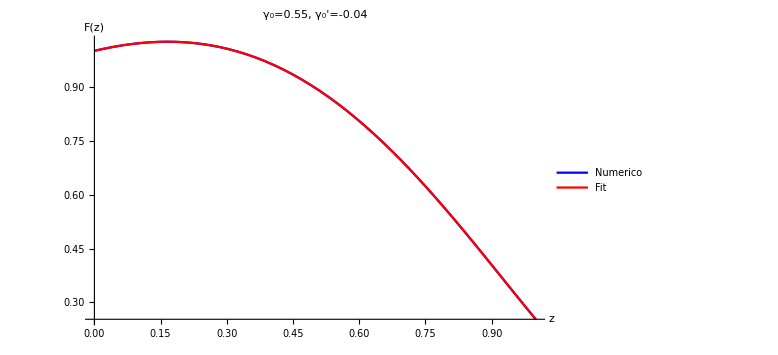

```mathematica
Show[p1,fit]
```

```mathematica
pointsfit4=Table[{z,fit4},{z,0,1,0.01}];
PearsonChiSquareTest[pointsfit4,points]
```

1.

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9998252471285074+0.29348225352019963 z-0.7648683711111824 z^2-0.4601092712354495 z^3-0.20474990376003904 z^4+0.38948688604832843 z^5
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

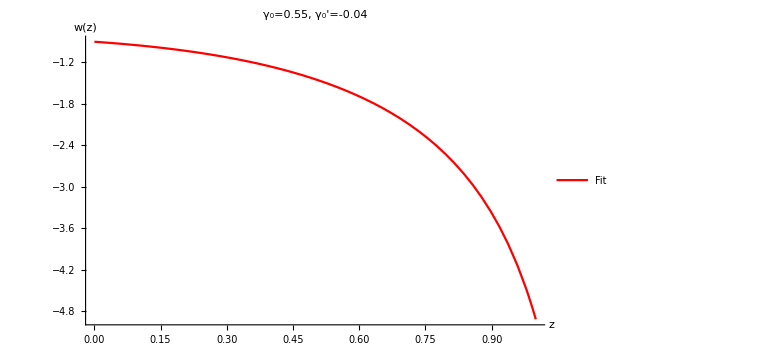

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

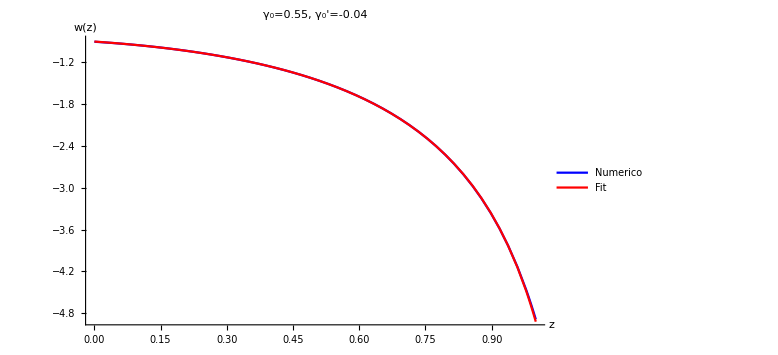

```mathematica
Show[wnum,wpol]
```

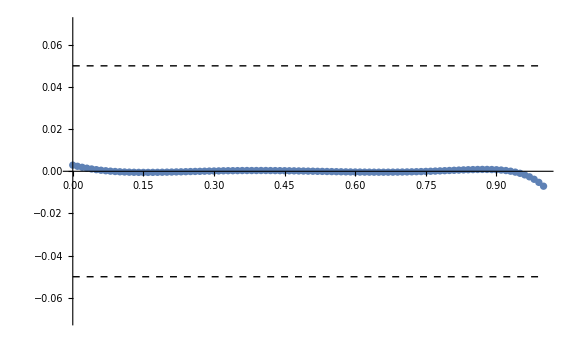

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
plotres=ListPlot[Res7];
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearCookies
ClearAttributes
```

ClearCookies

ClearAttributes

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma[a];
```

```mathematica
om=0.3;
gamma0=0.55;
gammap0=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

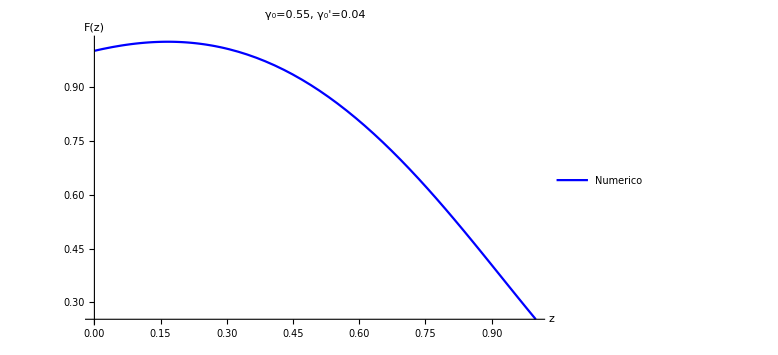

```mathematica
p1=Plot[Fz[z],{z,0,1}, PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

```mathematica
points=Table[{z,Fz[z]},{z,0,1,0.01}];
```

```mathematica
Fit[points, {1,z,z^2},z]
```

1.00128+0.336927 z-1.10728 z^2

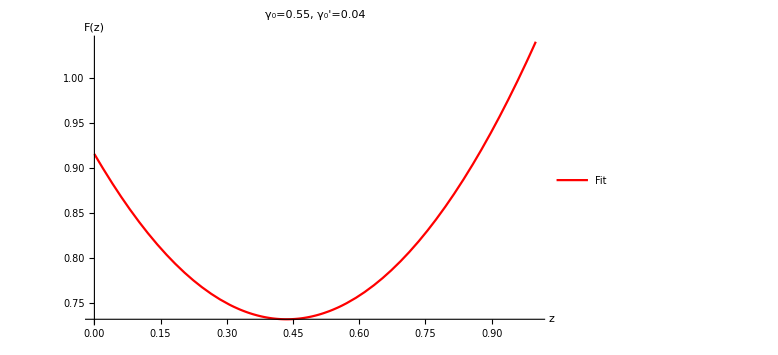

```mathematica
fit=Plot[0.9153030762604979-0.8447497780094505 z+0.9697331272863319 z^2,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

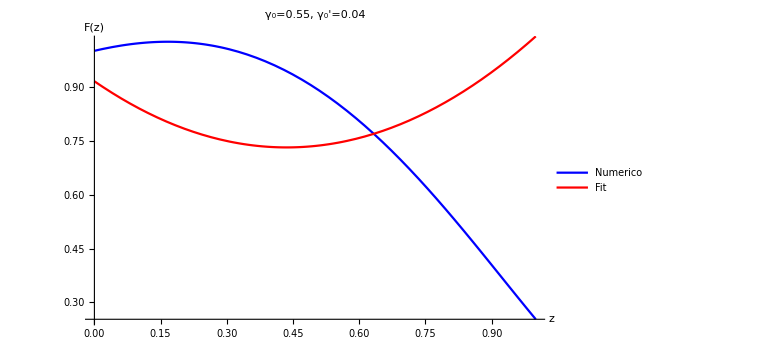

```mathematica
Show[p1,fit]
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9153030762604979-0.8447497780094505 z+0.9697331272863319 z^2
```

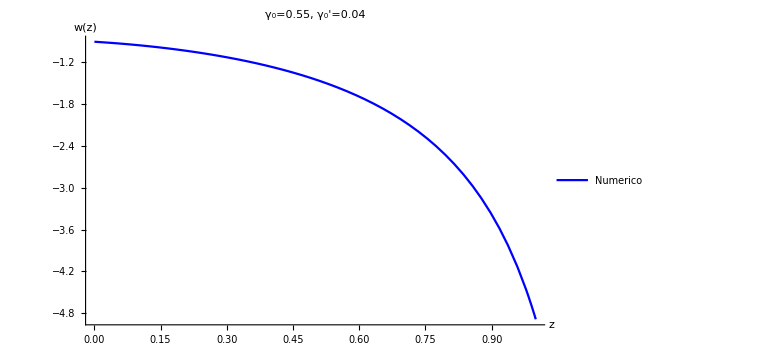

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

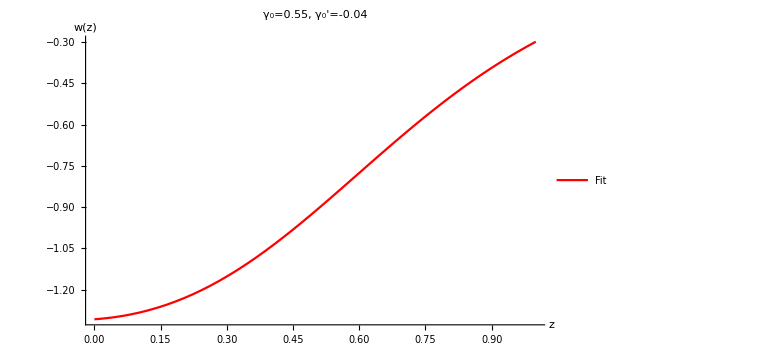

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

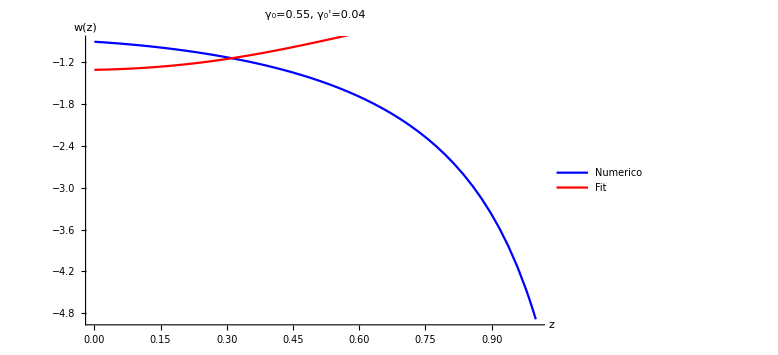

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

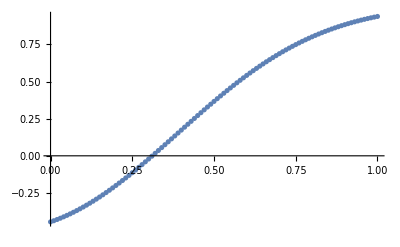

```mathematica
plotres=ListPlot[Res7]
```

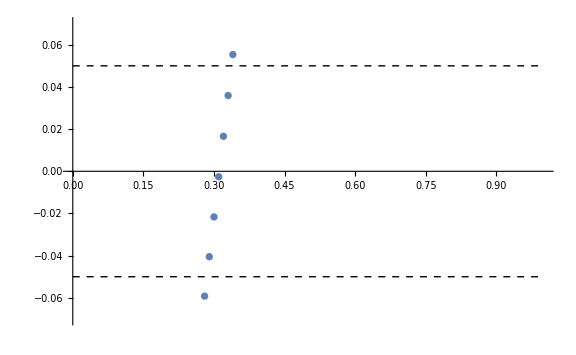

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
Fit[points, {1,z,z^2,z^3},z]
```

0.990883+0.464927 z-1.42888 z^2+0.214398 z^3

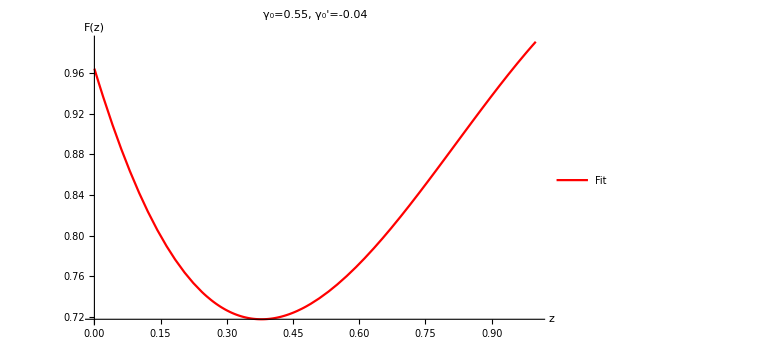

```mathematica
fit=Plot[0.9645313892263071-1.450610165699559 z+2.4919444125618084 z^2-1.0148075235169856 z^3,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=-0.04", Black, FontSize->20]]
```

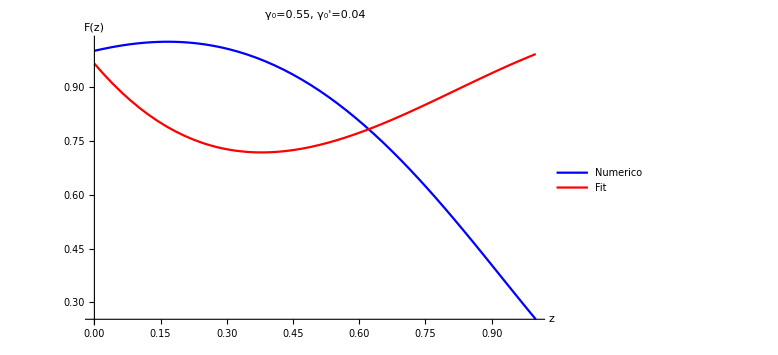

```mathematica
Show[p1,fit]
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9645313892263071-1.450610165699559 z+2.4919444125618084 z^2-1.0148075235169856 z^3
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

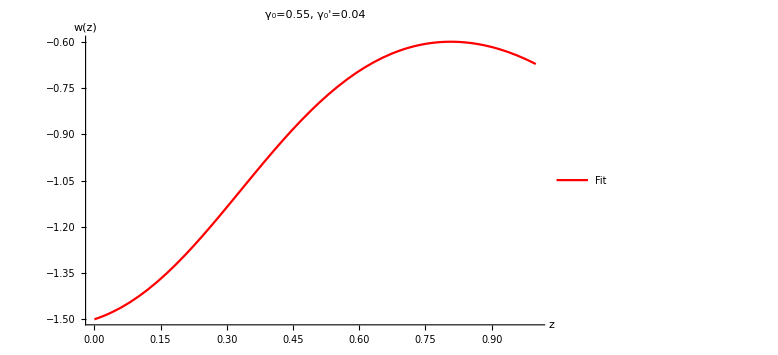

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

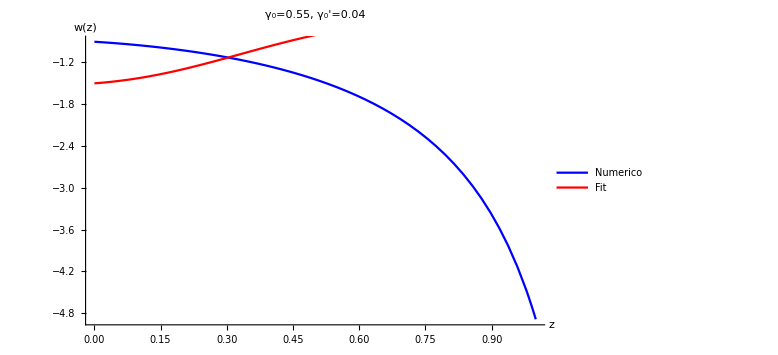

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

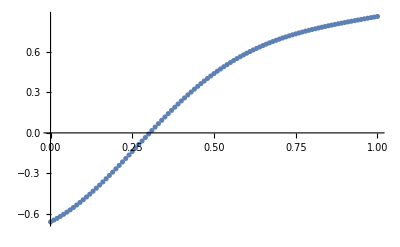

```mathematica
plotres=ListPlot[Res7]
```

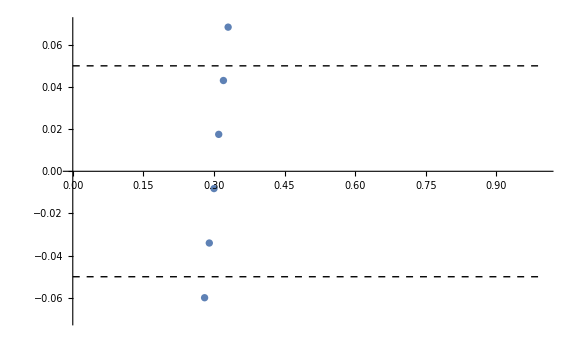

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
Fit[points, {1,z,z^2,z^3,z^4},z]
```

1.00122+0.248463 z-0.443444 z^2-1.32354 z^3+0.768967 z^4

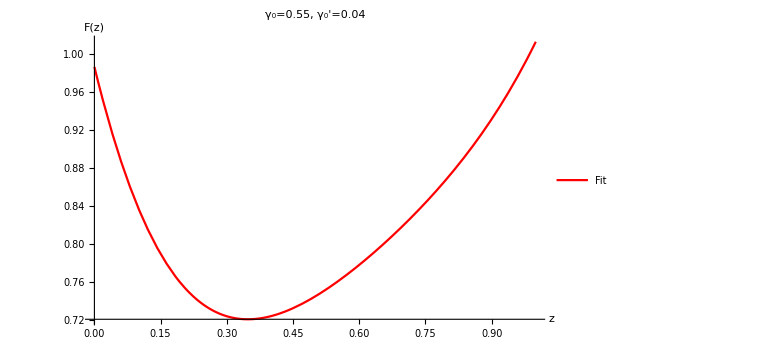

```mathematica
fit=Plot[0.9865659910002349-1.9119794103821057 z+4.592280778674371 z^2-4.292741766377022 z^3+1.6389671214300203 z^4,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

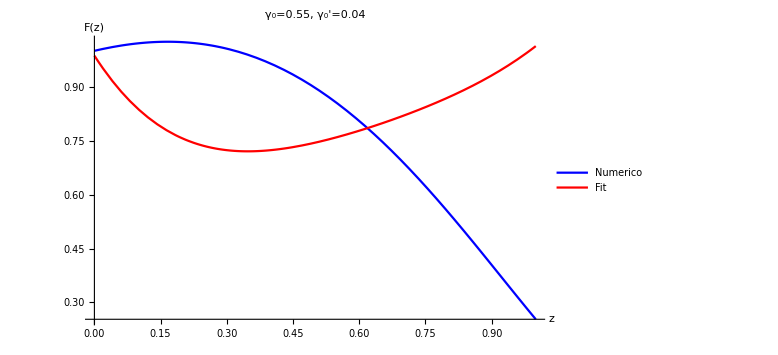

```mathematica
Show[p1,fit]
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9865659910002349-1.9119794103821057 z+4.592280778674371 z^2-4.292741766377022 z^3+1.6389671214300203 z^4
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

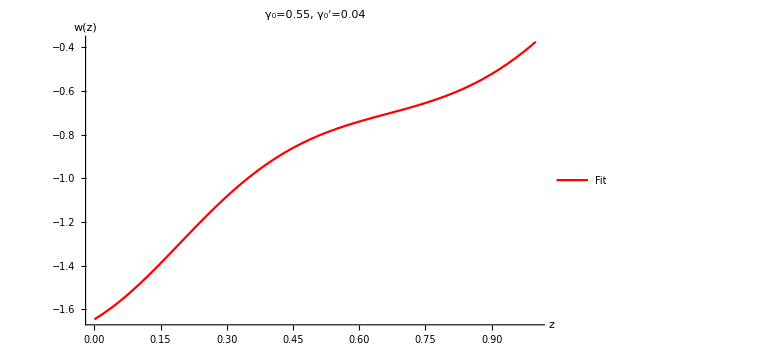

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

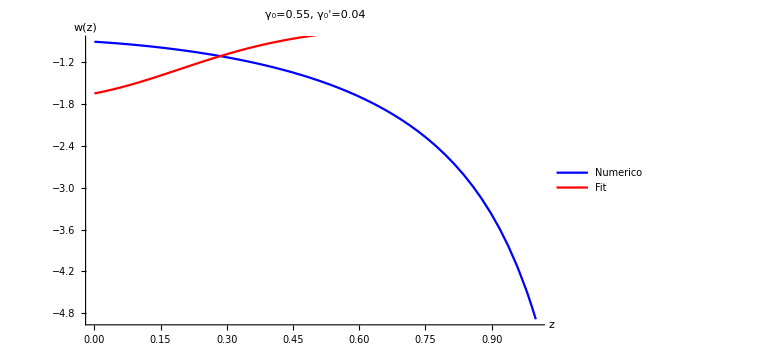

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

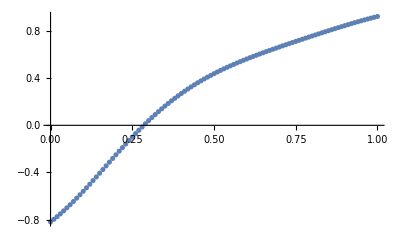

```mathematica
plotres=ListPlot[Res7]
```

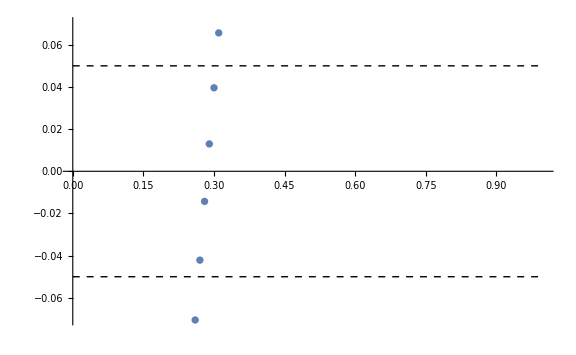

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```

```mathematica
Fit[points, {1,z,z^2,z^3,z^4,z^5},z]
```

0.999825+0.293482 z-0.764868 z^2-0.460109 z^3-0.20475 z^4+0.389487 z^5

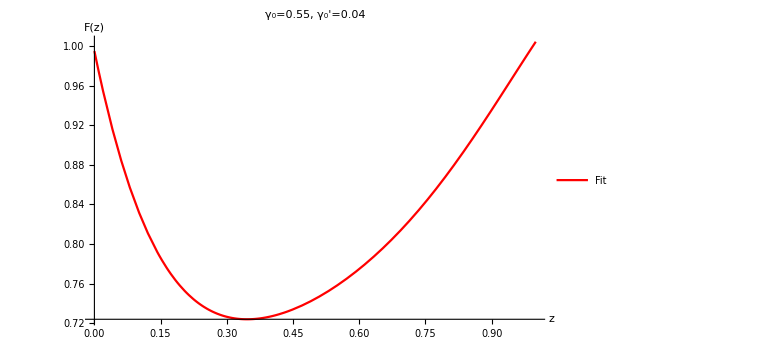

```mathematica
fit=Plot[0.9951313148859446-2.1881317546682935 z+6.563911724551258 z^2-9.589048584736883 z^3+7.611796403092957 z^4-2.3891317126651948 z^5,{z,0,1}, PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["F(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

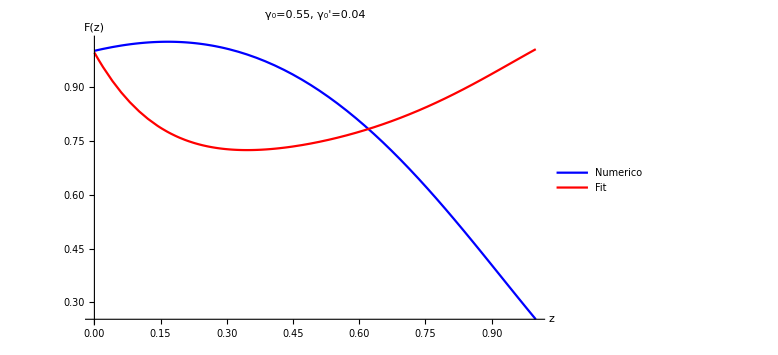

```mathematica
Show[p1,fit]
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
Fpoly[z_]:=0.9951313148859446-2.1881317546682935 z+6.563911724551258 z^2-9.589048584736883 z^3+7.611796403092957 z^4-2.3891317126651948 z^5
```

```mathematica
wnum=Plot[w[z],{z,0,1},PlotLegends->{"Numerico"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

-Graphics-

```mathematica
wpoly[z_]:=Fpoly'[z]/Fpoly[z] 1/3(1+z)-1;
```

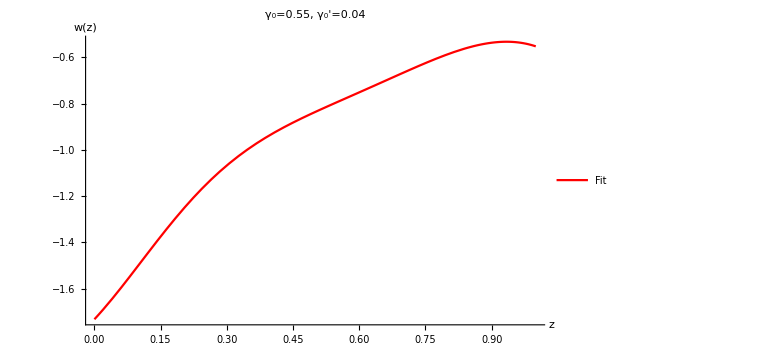

```mathematica
wpol=Plot[wpoly[z],{z,0,1},PlotLegends->{"Fit"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0=0.55, γ_0'=0.04", Black, FontSize->20]]
```

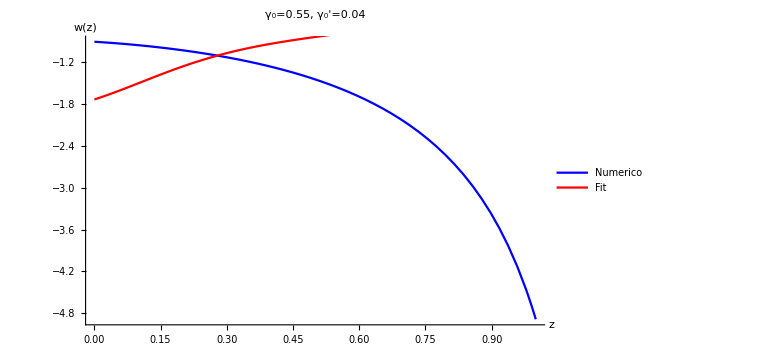

```mathematica
Show[wnum,wpol]
```

```mathematica
wnumtable=Table[{z,w[z]},{z,0,1,0.01}];
wpoltable=Table[{z,wpoly[z]},{z,0,1,0.01}];
```

```mathematica
dif1[z_]=1-wpoly[z]/w[z];
Res7=Table[{z,dif1[z]},{z,0,1,0.01}];
```

```mathematica
errorplot1=Plot[0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
errorplot2=Plot[-0.05,{z,0,1}, PlotStyle->{Thick, Dashed, Black}];
```

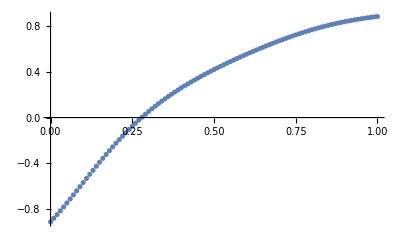

```mathematica
plotres=ListPlot[Res7]
```

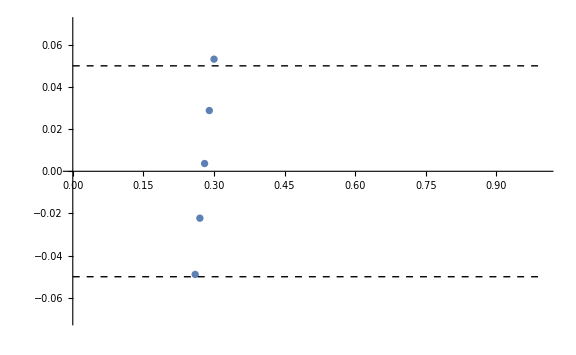

```mathematica
Show[plotres,errorplot1,errorplot2, PlotRange->{-0.07,0.07}, ImageSize->Large]
```